```mathematica
正负电荷产生的电力线——直接计算
```

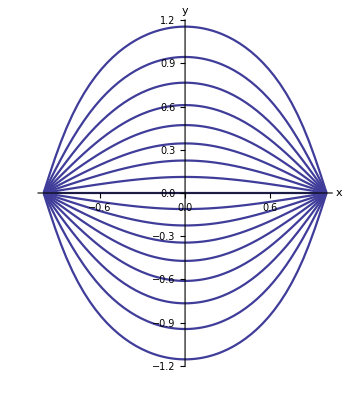

```mathematica
r=10.0^-3;a=1.0;q1=1;q2=-1;
ϕ[x_,y_]:=q1/(√((x-a)^2+y^2))+q2/(√((x+a)^2+y^2));
Ex=-D[ϕ[x,y],x];Ey=-D[ϕ[x,y],y];
k=(Ey/Ex)/.y->y[x];
θ1=π/2.0+π/10;θ2=3π/2.0-π/10;
equ={y'[x]==k,y[xstart]==ystart};
forceline={};
Do[
xstart=a+r*Cos[θ];ystart=r*Sin[θ];
xend=-(a-r);
s=NDSolve[equ,y,{x,xstart,xend}];
y=y/.s[[1]];
figure=Plot[y[x],{x,xstart,xend},
PlotStyle->Thickness[0.004],
AspectRatio->Automatic];
AppendTo[forceline,figure];
Clear[y],{θ,θ1,θ2,π/20}]
Show[forceline,PlotRange->All,
AxesStyle->Thickness[0.003],
AxesLabel->{"x","y"},
BaseStyle->{FontSize->13}]
Clear[ϕ,forceline,y,x,xstart,ystart]
```